```mathematica
(*Mathematica*)
```

```mathematica
(*m003(-3,1) extended)*)
p[z_]=ExpandAll[(z^3-z^2+1)*(z^2+z+1)]
```

1+z+z^5

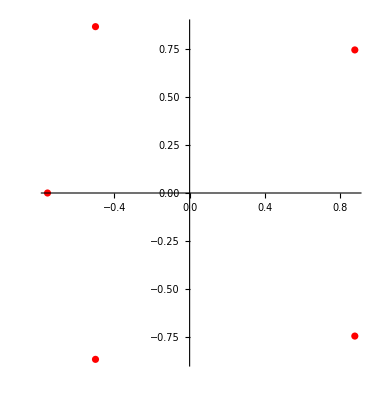

```mathematica
ComplexListPlot[z/.NSolve[p[z]==0,z],PlotStyle->Red]
```

```mathematica
ϕ=N[GoldenRatio]
r[i_]:=x/.NSolve[p[x]==0,x][[i]]
sc=2.0;
```

1.61803

```mathematica
f[z_]=Exp[2*π*I*ϕ]*z^10*(z^2-(sc*r[1])^2)*(z^2-(sc*r[2])^2)*(z^2-(sc*r[3])^2)*(z^2-(sc*r[4])^2)*(z^2-(sc*r[5])^2)/((-(sc*r[1]*z)^2+1)*(-(sc*r[2]*z)^2+1)*(-(sc*r[3]*z)^2+1)*(-(sc*r[4]*z)^2+1)*(-(sc*r[5]*z)^2+1));
```

```mathematica
g0=JuliaSetPlot[f[z],z, Method -> "OrbitDetection",ColorFunction->Hue,ImageSize->2000,PlotStyle->{PointSize[0.0005]},AspectRatio->1,ImageResolution->2000,PerformanceGoal->"Quality","Bound"->12,Frame->False,PlotRange->All];
```

#### 3D and plane Mandelbrots/ Julias

```mathematica
(*Julia with SQRT(x^2+y^2) limited measure*)
(*by Roger Lee .10Bagula 18 July 2023 © *)
numberOfz2ToEscape[z_] := Block[
	{escapeCount, nz = N[z],nn=4,nzold=0},
	For[
		escapeCount = 0,
		(Abs[nz]<64) && (escapeCount < 2048) &&(Abs[nz-nzold]>0.5*10^(-3)),
		nzold=nz;
		nz=f[nz];
		++escapeCount
	];
	
	escapeCount*If[(Abs[nz-nzold]>10^(-3)),escapeCount*(2*Pi-Abs[ArcTan[nz]+I*ArcTan[nz]*Tan[1]-Arg[z]]),escapeCount*(2*Pi-Arg[nz]*(Max[1-Arg[nz]/(2*Pi),Arg[nz]/(2*Pi)]))]
	
	
]
```

```mathematica
FractalPureM[{{ReMin_, ReMax_, ReSteps_},
			 {ImMin_, ImMax_, ImSteps_}}] :=
		ParallelTable[
			numberOfz2ToEscape[x + y I],
			{y, ImMin, ImMax, (ImMax - ImMin)/ImSteps},
			{x, ReMin, ReMax, (ReMax - ReMin)/ReSteps}
		
	]
```

```mathematica
arraym=FractalPureM[{{-2.75,2.75,1000},{-2.5,2.75,1000}}];
```

```mathematica
g1=ListPlot3D[N[Log[1/Max[arraym]+arraym]], Mesh -> False,AspectRatio -> Automatic,Boxed->False, Axes->False,ColorFunction->Hue,Background->Black,ViewPoint->Above,ImageSize->2000];
```

```mathematica
g2=ListDensityPlot[arraym,   Mesh -> False,     AspectRatio -> Automatic, ColorFunction->(Hue[(#^2/1.1)]&),ImageSize->2000,Axes->False,ImageSize->2000,Frame->False];
```

```mathematica
colortab=Reverse[Union[Sort[Join[Flatten[Delete[Sort[Union[Table[Delete[Sort[Union[Flatten[Table[If[i+j+k==n,{(1)^2,(1-j)^2,(1-k)^2},{}],{i,0,1,1/10},{j,0,1,1/10},{k,0,1,1/10}],2]]],1],{n,0,1,1/30}]]],1],1],{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}},{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/2,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/1.5,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/3,{{0,0,0.5625},{0,0,0.625},{0,0,0.6875},{0,0,0.75},{0,0,0.8125},{0,0,0.875},{0,0,0.9375},{0,0,1},{0,0.0625,1},{0,0.125,1},{0,0.1875,1},{0,0.25,1},{0,0.3125,1},{0,0.375,1},{0,0.4375,1},{0,0.5,1},{0,0.5625,1},{0,0.625,1},{0,0.6875,1},{0,0.75,1},{0,0.8125,1},{0,0.875,1},{0,0.9375,1},{0,1,1},{0.0625,1,1},{0.125,1,0.9375},{0.1875,1,0.875},{0.25,1,0.8125},{0.3125,1,0.75},{0.375,1,0.6875},{0.4375,1,0.625},{0.5,1,0.5625},{0.5625,1,0.5},{0.625,1,0.4375},{0.6875,1,0.375},{0.75,1,0.3125},{0.8125,1,0.25},{0.875,1,0.1875},{0.9375,1,0.125},{1,1,0.0625},{1,1,0},{1,0.9375,0},{1,0.875,0},{1,0.8125,0},{1,0.75,0},{1,0.6875,0},{1,0.625,0},{1,0.5625,0},{1,0.5,0},{1,0.4375,0},{1,0.375,0},{1,0.3125,0},{1,0.25,0},{1,0.1875,0},{1,0.125,0},{1,0.0625,0},{1,0,0},{0.9375,0,0},{0.875,0,0},{0.8125,0,0},{0.75,0,0},{0.6875,0,0},{0.625,0,0},{0.5625,0,0}}/6]]]];
```

```mathematica
Length[%]
```

383

```mathematica
cf[l_]:=Block[{niv,rgb},niv=If[l<1/319,1,Ceiling[383*l]];
rgb=colortab[[niv]];
RGBColor[rgb[[1]],rgb[[2]],rgb[[3]]]];
```

```mathematica
g3=Rasterize[ListDensityPlot[Abs[Log[1/Max[arraym]+arraym]], Mesh -> False, AspectRatio -> Automatic, ColorFunction->cf,ImageSize->2000,Frame->False],RasterSize->2000,ImageSize->2000];
```

```mathematica
Export["j_1000_m003_neg3_1_extended_z10_Herman_rings_3d_Inside_Outside_monitor_grid.jpg",GraphicsGrid[{{g0,g1},{g2,g3}},ImageSize->{{4000,4000}}]]
```

j_1000_m003_neg3_1_extended_z10_Herman_rings_3d_Inside_Outside_monitor_grid.jpg

```mathematica
(*end*)
```